## Huntington‒Hill Apportionment

Huntington‒Hill Method of Apportionment.
h is house size, p is a list of populations, g is a list of guaranteed seats.

```mathematica
HHRoundingFn=Function[x,Sqrt[(x-1)x]];
```

```mathematica
HHLowDivs=Function[{p,g,a},
Table[If[a[[i]]<g[[i]],∞,If[HHRoundingFn[a[[i]]+1]==0,∞,p[[i]]/HHRoundingFn[a[[i]]+1]]],
{i,1,Length[p]}
]
];
HHHighDivs=Function[{p,g,a},
Table[
If[a[[i]]<=g[[i]],∞,If[HHRoundingFn[a[[i]]]==0,∞,p[[i]]/HHRoundingFn[a[[i]]]]],
{i,1,Length[p]}
]
];
```

```mathematica
HHFoundCond=Function[{p,g,a},Max[HHLowDivs[p,g,a]]<=Min[HHHighDivs[p,g,a]]];
```

```mathematica
HHAddSet=Function[{p,g,a},Ordering[HHLowDivs[p,g,a],-1,NumericalOrder]];
HHDelSet=Function[{p,g,a},Ordering[HHHighDivs[p,g,a],1,NumericalOrder]];
```

```mathematica
DivisorMethodAllocation=Function[{d,p,g},
Module[{quota,geom},
quota:=g+p/d;
geom:=HHRoundingFn[Floor[#]+1]&/@quota;
MapThread[{m,q}|->Floor[q]+Boole[q>m],{geom,quota}]
]
];
```

```mathematica
HuntingtonHillApportionment=Function[{names,h,p,g},
MapThread[{#1,#2}&,
{names,
NestWhile[
x|->Module[{a,asum,nexta,priority,i,i2,k},
{a,asum,priority}=x;
i=Ordering[priority,-1,NumericalOrder][[1]];
i2=Ordering[priority,-2,NumericalOrder][[1]];
k:=p[[i]]/priority[[i2]];
(* We want to find the minimal x∈Integers s.t. p[[i]]/HHRoundingFn[x+1] <= priority[[i2]] && 0 <= x. After 0 this polynomial is increasin; thus it suffices to find x^2 + x == k and take the Floor[x+1] (effectively the ceiling, but going up when the priority is matched by another position).
*)
nexta=Min[Floor[-1/2+1/2 √(4 k^2+1)+1],h-asum+a[[i]]];
asum=asum+nexta-a[[i]];
a[[i]]=nexta;
priority[[i]]=If[HHRoundingFn[a[[i]]]==0,∞,p[[i]]/HHRoundingFn[a[[i]]+1]];
{a,asum,priority}
],
{g,Total[g],HHLowDivs[p,g,g]},
x|->x[[2]]<h
][[1]]
}
]
];
```

## House Size, Electors, and Voter Power

### The Current House and Electors

#### Census Data

USA state populations from the 2020 census.
https://www.census.gov/data/tables/time-series/demo/popest/2020s-state-total.html

```mathematica
usaPopulationDataCSV=FileNameJoin[{NotebookDirectory[],"NST-EST2022-ALLDATA.csv"}];
usaPopulationData=Import[usaPopulationDataCSV,"Dataset",HeaderLines->1];
```

```mathematica
usaPopulationData1960CSV=FileNameJoin[{NotebookDirectory[],"1960-DATA.csv"}];
usaPopulationData1960=Import[usaPopulationData1960CSV,"Dataset",HeaderLines->1];
```

```mathematica
usaPopulationData1960
```

Select out the states that actually get house seats.

```mathematica
usa50States={"Alabama","Alaska","Arizona","Arkansas","California","Colorado","Connecticut","Delaware","Florida","Georgia","Hawaii","Idaho","Illinois","Indiana","Iowa","Kansas","Kentucky","Louisiana","Maine","Maryland","Massachusetts","Michigan","Minnesota","Mississippi","Missouri","Montana","Nebraska","Nevada","New Hampshire","New Jersey","New Mexico","New York","North Carolina","North Dakota","Ohio","Oklahoma","Oregon","Pennsylvania","Rhode Island","South Carolina","South Dakota","Tennessee","Texas","Utah","Vermont","Virginia","Washington","West Virginia","Wisconsin","Wyoming"};
```

```mathematica
usa50StatePopData={#["NAME"],#["POPESTIMATE2020"]}&/@Select[
usaPopulationData[All,{"NAME","POPESTIMATE2020"}],
r|->MemberQ[usa50States,r["NAME"]]
]//Normal;
```

```mathematica
usa50StateAndDCPopData={#["NAME"],#["POPESTIMATE2020"]}&/@Select[
usaPopulationData[All,{"NAME","POPESTIMATE2020"}],
r|->MemberQ[usa50States,r["NAME"]]||r["NAME"]=="District of Columbia"
]//Normal;
```

```mathematica
smallest15States=#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],15]
```

{Wyoming,Vermont,Alaska,North Dakota,South Dakota,Delaware,Montana,Rhode Island,Maine,New Hampshire,Hawaii,West Virginia,Idaho,Nebraska,New Mexico}

```mathematica
largest5Smallest5States=Join[#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],5],#[[1]]&/@Take[SortBy[usa50StatePopData,#[[2]]&],-5]];
```

```mathematica
totalPop50States=Fold[#1+#2[[2]]&,0,usa50StateAndDCPopData];
totalPop50StatesAndDC=Fold[#1+#2[[2]]&,0,usa50StateAndDCPopData];
```

```mathematica
usa50StateAndDCPopFraction=
({#[[1]],N[#[[2]]/Total[#[[2]]&/@usa50StateAndDCPopData],6]})&/@usa50StateAndDCPopData
```

{{Alabama,0.015177},{Alaska,0.00221085},{Arizona,0.0216582},{Arkansas,0.00909228},{California,0.119156},{Colorado,0.01745},{Connecticut,0.0108514},{Delaware,0.0029927},{District of Columbia,0.00202366},{Florida,0.0651247},{Georgia,0.0323664},{Hawaii,0.00437705},{Idaho,0.00557809},{Illinois,0.0385705},{Indiana,0.0204783},{Iowa,0.00962431},{Kansas,0.00886219},{Kentucky,0.0135966},{Louisiana,0.0140317},{Maine,0.00411315},{Maryland,0.0186214},{Massachusetts,0.0211025},{Michigan,0.0303747},{Minnesota,0.0172237},{Mississippi,0.00892319},{Missouri,0.0185635},{Montana,0.00327915},{Nebraska,0.00592028},{Nevada,0.00939831},{New Hampshire,0.00415849},{New Jersey,0.0279679},{New Mexico,0.00639009},{New York,0.0606564},{North Carolina,0.0315206},{North Dakota,0.00235141},{Ohio,0.0355871},{Oklahoma,0.0119601},{Oregon,0.0128044},{Pennsylvania,0.0391976},{Rhode Island,0.00330711},{South Carolina,0.0154802},{South Dakota,0.00267803},{Tennessee,0.020891},{Texas,0.0881794},{Utah,0.00990549},{Vermont,0.00193928},{Virginia,0.0260518},{Washington,0.0232994},{West Virginia,0.00540379},{Wisconsin,0.017786},{Wyoming,0.00174234}}

#### The House

Let’s replicate the current house and electoral college to make sure our calculations are right.

```mathematica
usaHouseSize2020=435;
```

```mathematica
usaHouse2020=HuntingtonHillApportionment[(#[[2]]&/@usa50StatePopData),usaHouseSize2020,(#[[2]]&/@usa50StatePopData),Table[1,{i,1,50}]]
```

{{5031362,7},{732923,1},{7179943,9},{3014195,4},{39501653,52},{5784865,8},{3597362,5},{992114,1},{21589602,28},{10729828,14},{1451043,2},{1849202,2},{12786580,17},{6788799,9},{3190571,4},{2937919,4},{4507445,6},{4651664,6},{1363557,2},{6173205,8},{6995729,9},{10069577,13},{5709852,8},{2958141,4},{6153998,8},{1087075,2},{1962642,3},{3115648,4},{1378587,2},{9271689,12},{2118390,3},{20108296,26},{10449445,14},{779518,1},{11797517,15},{3964912,5},{4244795,6},{12994440,17},{1096345,2},{5131848,7},{887799,1},{6925619,9},{29232474,38},{3283785,4},{642893,1},{8636471,11},{7724031,10},{1791420,2},{5896271,8},{577605,1}}

Which is correct!

The 23rd amendment is a little vague on how to calculate how many electors DC is entitled to. The text states DC is to have electors equal to the number of senators and representatives it “would be entitled if it were a State, but in no event more than the least populous State”.

My interpretation is that you have to run a whole new apportionment for the house, with DC included. This is what I do next.

```mathematica
USAElectors=Function[{h},
Module[{house,houseWithDC,stateElectors,dcElectors},
house:=HuntingtonHillApportionment[(#[[1]]&/@usa50StatePopData),h,(#[[2]]&/@usa50StatePopData),Table[1,{i,1,50}]];
houseWithDC:=HuntingtonHillApportionment[(#[[1]]&/@usa50StateAndDCPopData),h,(#[[2]]&/@usa50StateAndDCPopData),Table[1,{i,1,51}]];
stateElectors:=({#[[1]],#[[2]]+2})&/@house;(*plus two for the state senators *);
dcElectors:=Min[
Min[#[[2]]&/@stateElectors],
SelectFirst[houseWithDC,(e|->e[[1]]=="District of Columbia")][[2]]+2
];
Append[stateElectors, {"District of Columbia", dcElectors}] (* Add in DC as per the 23rd amendment *)
]
];
```

```mathematica
usaElectors2022=USAElectors[usaHouseSize2020]
```

{{Alabama,9},{Alaska,3},{Arizona,11},{Arkansas,6},{California,54},{Colorado,10},{Connecticut,7},{Delaware,3},{Florida,30},{Georgia,16},{Hawaii,4},{Idaho,4},{Illinois,19},{Indiana,11},{Iowa,6},{Kansas,6},{Kentucky,8},{Louisiana,8},{Maine,4},{Maryland,10},{Massachusetts,11},{Michigan,15},{Minnesota,10},{Mississippi,6},{Missouri,10},{Montana,4},{Nebraska,5},{Nevada,6},{New Hampshire,4},{New Jersey,14},{New Mexico,5},{New York,28},{North Carolina,16},{North Dakota,3},{Ohio,17},{Oklahoma,7},{Oregon,8},{Pennsylvania,19},{Rhode Island,4},{South Carolina,9},{South Dakota,3},{Tennessee,11},{Texas,40},{Utah,6},{Vermont,3},{Virginia,13},{Washington,12},{West Virginia,4},{Wisconsin,10},{Wyoming,3},{District of Columbia,3}}

```mathematica
Total[#[[2]]&/@usaElectors2022]
```

538

And we get 538, which is what we expect.

### Varying The House Size

Here’s a table on the total number of electors we get when we vary the size of the house.

```mathematica
electorsAtDifferentSizes=(n|->{n,USAElectors[n]})/@Sort[Append[Table[n,{n,400,4000,100}],435]];
```

```mathematica
numberOfElectors=Dataset[
Association@Prepend[Prepend[(#[[1]]->#[[2]]&/@#[[2]]),"total"->Total[#[[2]]&/@#[[2]]]],"n"->#[[1]]]&/@electorsAtDifferentSizes
];
```

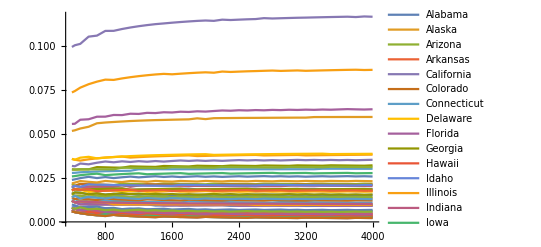

```mathematica
fractionOfElectors=(r|->Prepend[(N[#/r[["total"]],6])&/@KeyDrop[r,{"total","n"}],"n"->r[["n"]]])/@numberOfElectors;
ListPlot[Transpose[KeyDrop[(r|->({r[["n"]],#}&/@r))/@fractionOfElectors,{"n"}]],Joined->True,PlotRange->All]
```

### Plain Relative Proportionality

If we want, we can compare fraction of the population to fraction of the.
But note this is a bad measure, as the electors don’t get to free vote. We’ll get into better ways to measure voting power in the next section.

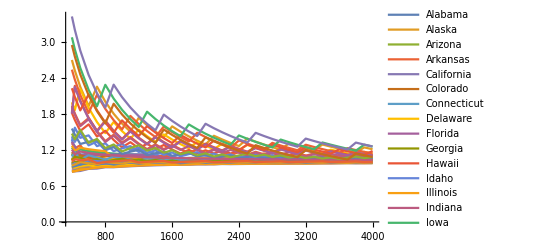

```mathematica
relativeProportionalityCoords=Dataset[(r|->
Merge[
{KeyDrop[r,{"total","n"}],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[["n"]],#[[1]]/#[[2]]}&
]
)/@fractionOfElectors];
ListPlot[Transpose[relativeProportionalityCoords],Joined->True,PlotRange->All,PlotLegends->Automatic]
```

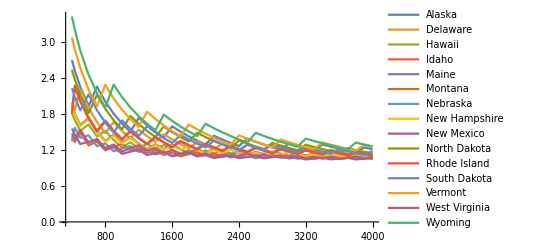

```mathematica
relativeProportionalityCoords=Dataset[(r|->
Merge[
{KeyDrop[r,{"total","n"}],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[["n"]],#[[1]]/#[[2]]}&
]
)/@fractionOfElectors];
ListPlot[
KeySelect[Transpose[relativeProportionalityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All,PlotLegends->Automatic]
```

## Electoral Power

Now, the problem with this is we can’t just take the fraction, and divide it by the population of each state, and say “this is unfair because the proportion of electors is not equal to the proportion of population” because all states (except Maine and Nebraska) vote at large; that is every elector for that state votes for the single winner for their state.
  Thus in fact the correct way to analyse this problem is as a system of majority voting where the participants (the states) have differently weighted votes.

### Indices of Power

#### Banzhaf Index

```mathematica
(* Uno's algorithm for computing the Banzhaf index.
(Takeaki Uno, 2012, Efficient Computation of Power Indices for Weighted Majority Games) *)
BanzhafIndex=Function[ws,
Module[{quota,maxcol,iws,l,u,usum,out},
quota=Ceiling[(Total[ws]+1)/2];
(* As the update steps for l and u only 'reach back' by the maximum weight less than or equal to the quota, this quantity bounds the total length of rows. An appropriate bound is to assume that the maximum weight is used on every step, thus we get Length[ws] increases of the maximum weight at the final row. *);
maxcol=Min[quota-1,Length[ws]*Max[Select[ws,#<=quota&]]];
l=#[[1]]&/@NestWhileList[
ri|->Module[{r,i},
{r,i}=ri;
{Table[
r[[y+1]]+If[y<ws[[i]],0,r[[y-ws[[i]]+1]]],
{y,0,maxcol}
],
i+1}
],
{Table[Boole[y==0],{y,0,maxcol}],1},
ri|->ri[[2]]<Length[ws]
];
u=Reverse[#[[1]]&/@NestWhileList[
ri|->Module[{r,i},
{r,i}=ri;
{Table[
r[[y+1]]+If[y<ws[[i]],0,r[[y-ws[[i]]+1]]],
{y,0,maxcol}
],i-1}
],
{Table[Boole[y==0],{y,0,maxcol}],Length[ws]},
ri|->1<ri[[2]]
]];
usum=FoldList[Plus,Table[0,{x,1,Length[u]}],Transpose[u]];
Table[
Sum[
l[[i,z+1]]*(usum[[Min[quota-z,maxcol+1]+1,i]]-usum[[Min[Max[quota-ws[[i]]-z,0],maxcol+1]+1,i]]),
{z,0,maxcol}
],
{i,1,Length[ws]}
]
]
];
```

```mathematica
BanzhafIndex[{1,1,4,6}]
```

{1,1,1,7}

```mathematica
(* The Banzhaf index of a vector of all 1s; same for all entries, so it just returns the number.
Recall that the Banzhaf index of voter i is the number of coalitions (subsets) which meet quota, but would not meet quota if i was removed. Recall the quota is Ceiling[(n+1)/2].
As i contributes 1, the number of coalitions which meet quota, for which i is decisive is the subsets which are of size Ceiling[(n+1)/2]-1, chosen from all voters except i (i.e. n-1 of them).
Note that Ceiling[(n+1)/2]-1 == Floor[n/2] for the integers.
*)
UniformBanzhafIndex=Function[n,Binomial[n-1,Floor[(n-1)/2]]];
```

```mathematica
(* Even: k=2*n, Binomial[2*n-1,n - 1] = Prod[(2n-i)/i,{i,1,n-1}] = ((2n-1)!)/((n-1)!(n)!)
Odd: k=2*n+1, Binomial[2*n,n] = Prod[(2n+1-i)/i,{i,1,n}] = ((2n)!)/(n!)^2
*)
```

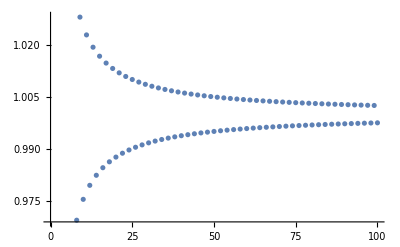

```mathematica
(* Unfortunately, the binomial function is very slow to calculate for large numbers (like the population of a state).
Thus here we use the approximation Binomial[2n,n] ~ 2^(2n)/Sqrt[n Pi].
*)
UniformAbsoluteBanzhafIndexApproximation=Function[n,1/(√(2*π*n))];
ListPlot[Table[{n,(UniformBanzhafIndex[n]/2^n)/UniformAbsoluteBanzhafIndexApproximation[n]},{n,1,100,1}]]
```

For example, the error at the number of population in the smallest state (Wyoming) is about 2×10^-10, and the error decreases as the number gets larger. The probabilities that come out of our problem are small, but still orders of magnitude larger than that, so it’s perfectly fine to use it for our problem.

```mathematica
N[UniformAbsoluteBanzhafIndexApproximation[577605]-UniformBanzhafIndex[577605]/2^577605]
```

-2.27198×10^-10

### Power per State

#### Banzhaf Index

```mathematica
electorsBanzhafCount=(r|->
Module[{n,states,electors,bzfidx},
{n,states}=r;
electors=#[[2]]&/@states;
bzfidx=BanzhafIndex[electors];
{n,Length[electors],Association@MapThread[#1[[1]]->#2&,{states,bzfidx}]}
]
)/@electorsAtDifferentSizes;
```

```mathematica
electorsAbsoluteBanzhafIndex={#[[1]],(c|->c/2^(#[[2]]))/@#[[3]]}&/@electorsBanzhafCount;
electorsNormalisedBanzhafIndex={#[[1]],(c|->c/Total[#[[3]]])/@#[[3]]}&/@electorsBanzhafCount;
```

Now, we can compare the relative proportionality of the size of the state to its power to affect the outcome of the vote.

```mathematica
relativePowerProportionalityCoords=Dataset[(r|->
Merge[
{r[[2]],Association@((#[[1]]->#[[2]])&/@usa50StateAndDCPopFraction)},
{r[[1]],#[[1]]/#[[2]]}&
]
)/@electorsNormalisedBanzhafIndex];
```

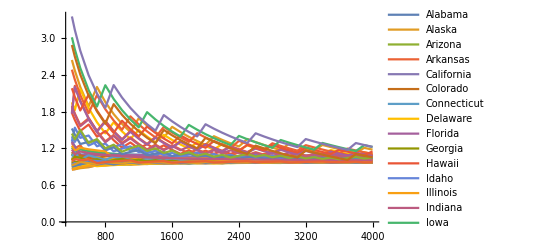

```mathematica
ListPlot[
Transpose[relativePowerProportionalityCoords],
Joined->True,PlotRange->All
]
```

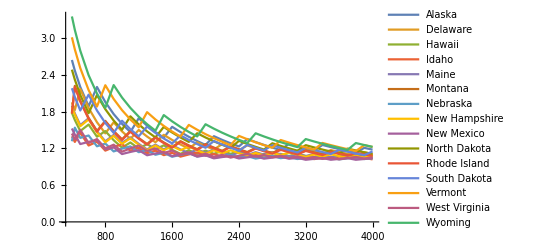

```mathematica
ListPlot[
KeySelect[Transpose[relativePowerProportionalityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

### Power per Voter in a State

What is the probability that any particular voter is in a coalition that is decisive, and that voter is decisive?

```mathematica
uniformVoterDecisiveProbability=UniformAbsoluteBanzhafIndexApproximation[totalPop50StatesAndDC];
```

```mathematica
N[uniformVoterDecisiveProbability]
```

0.0000219109

```mathematica
voterInStateDecisiveProbability=
Association[(nr|->
nr[[1]]->Merge[{
nr[[2]],
Association@(Apply[Rule]/@usa50StateAndDCPopData)
},#[[1]]*UniformAbsoluteBanzhafIndexApproximation[#[[2]]]&
]
)/@electorsAbsoluteBanzhafIndex];
```

```mathematica
voterInStateDecisiveProbabilityCoords=
Dataset[KeyValueMap[
({n,r}|->
{n,#}&/@r
),
voterInStateDecisiveProbability
]];
```

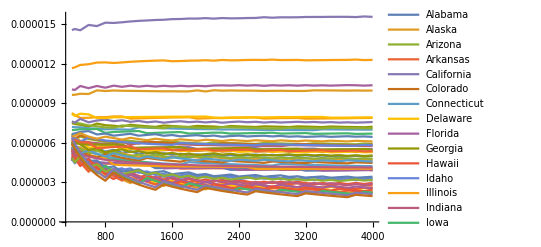

```mathematica
ListPlot[
Transpose[voterInStateDecisiveProbabilityCoords],
Joined->True,PlotRange->All
]
```

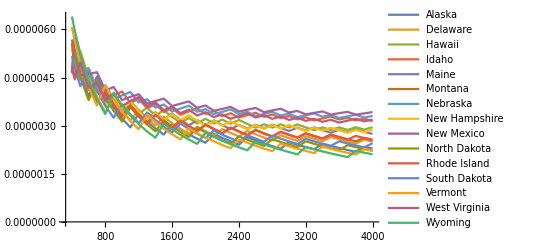

```mathematica
ListPlot[
KeySelect[Transpose[voterInStateDecisiveProbabilityCoords],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

```mathematica
ListPlot[
KeySelect[Transpose[voterInStateDecisiveProbabilityCoords],MemberQ[largest5Smallest5States,#]&],
Joined->True,PlotRange->All,PlotLegends->Automatic
]
```

Voter Decisive Vote Probability of the 5 Largest and 5 Smallest States

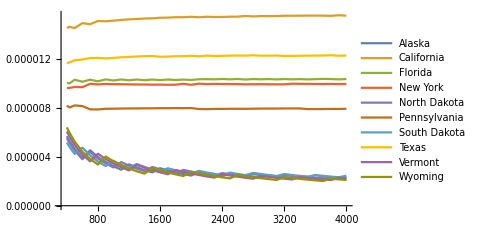

```mathematica
comparativeVoterInStateDecisiveProbability=
(r|->Outer[N[#1/#2,3]&,Values[r],Values[r]])/@voterInStateDecisiveProbability;
```

```mathematica
TableForm[
comparativeVoterInStateDecisiveProbability[435],
TableHeadings->{Keys[voterInStateDecisiveProbability[435]],Keys[voterInStateDecisiveProbability[435]]}
]
```

| Alabama | Alaska | Arizona | Arkansas | California | Colorado | Connecticut | Delaware | Florida | Georgia | Hawaii | Idaho | Illinois | Indiana | Iowa | Kansas | Kentucky | Louisiana | Maine | Maryland | Massachusetts | Michigan | Minnesota | Mississippi | Missouri | Montana | Nebraska | Nevada | New Hampshire | New Jersey | New Mexico | New York | North Carolina | North Dakota | Ohio | Oklahoma | Oregon | Pennsylvania | Rhode Island | South Carolina | South Dakota | Tennessee | Texas | Utah | Vermont | Virginia | Washington | West Virginia | Wisconsin | Wyoming | District of Columbia
Alabama | 1. | 1.15 | 0.976 | 1.16 | 0.415 | 0.965 | 1.09 | 1.33 | 0.606 | 0.817 | 1.21 | 1.37 | 0.749 | 0.949 | 1.2 | 1.15 | 1.07 | 1.08 | 1.17 | 0.996 | 0.964 | 0.845 | 0.958 | 1.15 | 0.995 | 1.05 | 1.13 | 1.18 | 1.18 | 0.87 | 1.17 | 0.629 | 0.807 | 1.18 | 0.806 | 1.14 | 1.03 | 0.755 | 1.05 | 1.01 | 1.26 | 0.959 | 0.518 | 1.21 | 1.07 | 0.905 | 0.928 | 1.34 | 0.974 | 1.02 | 1.1
Alaska | 0.872 | 1. | 0.851 | 1.01 | 0.362 | 0.841 | 0.948 | 1.16 | 0.529 | 0.712 | 1.06 | 1.19 | 0.653 | 0.827 | 1.04 | 1. | 0.929 | 0.943 | 1.02 | 0.868 | 0.84 | 0.737 | 0.835 | 1. | 0.867 | 0.913 | 0.981 | 1.03 | 1.03 | 0.758 | 1.02 | 0.549 | 0.703 | 1.03 | 0.702 | 0.996 | 0.901 | 0.658 | 0.917 | 0.88 | 1.1 | 0.836 | 0.451 | 1.06 | 0.937 | 0.789 | 0.809 | 1.17 | 0.849 | 0.888 | 0.957
Arizona | 1.02 | 1.18 | 1. | 1.19 | 0.425 | 0.988 | 1.11 | 1.37 | 0.621 | 0.837 | 1.24 | 1.4 | 0.767 | 0.972 | 1.23 | 1.18 | 1.09 | 1.11 | 1.2 | 1.02 | 0.987 | 0.866 | 0.982 | 1.18 | 1.02 | 1.07 | 1.15 | 1.21 | 1.21 | 0.891 | 1.2 | 0.645 | 0.826 | 1.21 | 0.825 | 1.17 | 1.06 | 0.774 | 1.08 | 1.03 | 1.29 | 0.982 | 0.53 | 1.24 | 1.1 | 0.927 | 0.95 | 1.38 | 0.997 | 1.04 | 1.12
Arkansas | 0.86 | 0.987 | 0.84 | 1. | 0.357 | 0.83 | 0.936 | 1.15 | 0.522 | 0.703 | 1.04 | 1.18 | 0.644 | 0.817 | 1.03 | 0.987 | 0.916 | 0.931 | 1.01 | 0.857 | 0.829 | 0.727 | 0.824 | 0.991 | 0.856 | 0.901 | 0.969 | 1.02 | 1.01 | 0.748 | 1.01 | 0.541 | 0.694 | 1.02 | 0.693 | 0.983 | 0.889 | 0.65 | 0.905 | 0.869 | 1.09 | 0.825 | 0.445 | 1.04 | 0.924 | 0.778 | 0.798 | 1.16 | 0.838 | 0.876 | 0.944
California | 2.41 | 2.77 | 2.35 | 2.8 | 1. | 2.32 | 2.62 | 3.22 | 1.46 | 1.97 | 2.92 | 3.29 | 1.81 | 2.29 | 2.88 | 2.77 | 2.57 | 2.61 | 2.83 | 2.4 | 2.32 | 2.04 | 2.31 | 2.78 | 2.4 | 2.53 | 2.71 | 2.85 | 2.84 | 2.1 | 2.82 | 1.52 | 1.94 | 2.85 | 1.94 | 2.75 | 2.49 | 1.82 | 2.54 | 2.43 | 3.04 | 2.31 | 1.25 | 2.92 | 2.59 | 2.18 | 2.24 | 3.24 | 2.35 | 2.46 | 2.65
Colorado | 1.04 | 1.19 | 1.01 | 1.21 | 0.43 | 1. | 1.13 | 1.38 | 0.629 | 0.847 | 1.26 | 1.42 | 0.777 | 0.984 | 1.24 | 1.19 | 1.1 | 1.12 | 1.22 | 1.03 | 0.999 | 0.876 | 0.993 | 1.19 | 1.03 | 1.09 | 1.17 | 1.23 | 1.22 | 0.902 | 1.21 | 0.653 | 0.836 | 1.23 | 0.836 | 1.18 | 1.07 | 0.783 | 1.09 | 1.05 | 1.31 | 0.994 | 0.537 | 1.26 | 1.11 | 0.938 | 0.962 | 1.39 | 1.01 | 1.06 | 1.14
Connecticut | 0.919 | 1.05 | 0.897 | 1.07 | 0.381 | 0.886 | 1. | 1.23 | 0.557 | 0.751 | 1.11 | 1.26 | 0.688 | 0.872 | 1.1 | 1.05 | 0.979 | 0.995 | 1.08 | 0.916 | 0.886 | 0.777 | 0.881 | 1.06 | 0.914 | 0.963 | 1.03 | 1.09 | 1.08 | 0.799 | 1.08 | 0.578 | 0.741 | 1.09 | 0.741 | 1.05 | 0.95 | 0.694 | 0.967 | 0.928 | 1.16 | 0.881 | 0.476 | 1.12 | 0.987 | 0.832 | 0.853 | 1.24 | 0.895 | 0.936 | 1.01
Delaware | 0.749 | 0.86 | 0.731 | 0.871 | 0.311 | 0.723 | 0.815 | 1. | 0.454 | 0.612 | 0.907 | 1.02 | 0.561 | 0.711 | 0.896 | 0.86 | 0.798 | 0.811 | 0.879 | 0.746 | 0.722 | 0.633 | 0.718 | 0.863 | 0.745 | 0.785 | 0.844 | 0.885 | 0.884 | 0.652 | 0.876 | 0.472 | 0.604 | 0.886 | 0.604 | 0.856 | 0.774 | 0.566 | 0.788 | 0.757 | 0.946 | 0.718 | 0.388 | 0.909 | 0.805 | 0.678 | 0.695 | 1.01 | 0.73 | 0.763 | 0.822
Florida | 1.65 | 1.89 | 1.61 | 1.92 | 0.684 | 1.59 | 1.79 | 2.2 | 1. | 1.35 | 2. | 2.25 | 1.24 | 1.57 | 1.97 | 1.89 | 1.76 | 1.78 | 1.93 | 1.64 | 1.59 | 1.39 | 1.58 | 1.9 | 1.64 | 1.73 | 1.86 | 1.95 | 1.95 | 1.43 | 1.93 | 1.04 | 1.33 | 1.95 | 1.33 | 1.88 | 1.7 | 1.25 | 1.73 | 1.67 | 2.08 | 1.58 | 0.854 | 2. | 1.77 | 1.49 | 1.53 | 2.22 | 1.61 | 1.68 | 1.81
Georgia | 1.22 | 1.4 | 1.19 | 1.42 | 0.508 | 1.18 | 1.33 | 1.63 | 0.742 | 1. | 1.48 | 1.67 | 0.917 | 1.16 | 1.46 | 1.4 | 1.3 | 1.32 | 1.44 | 1.22 | 1.18 | 1.03 | 1.17 | 1.41 | 1.22 | 1.28 | 1.38 | 1.45 | 1.44 | 1.06 | 1.43 | 0.77 | 0.987 | 1.45 | 0.986 | 1.4 | 1.26 | 0.924 | 1.29 | 1.24 | 1.54 | 1.17 | 0.633 | 1.48 | 1.31 | 1.11 | 1.13 | 1.65 | 1.19 | 1.25 | 1.34
Hawaii | 0.826 | 0.948 | 0.807 | 0.96 | 0.343 | 0.797 | 0.899 | 1.1 | 0.501 | 0.675 | 1. | 1.13 | 0.619 | 0.784 | 0.988 | 0.948 | 0.88 | 0.894 | 0.969 | 0.823 | 0.796 | 0.698 | 0.792 | 0.951 | 0.822 | 0.866 | 0.93 | 0.976 | 0.975 | 0.719 | 0.966 | 0.52 | 0.666 | 0.977 | 0.666 | 0.944 | 0.854 | 0.624 | 0.869 | 0.834 | 1.04 | 0.792 | 0.428 | 1. | 0.888 | 0.747 | 0.766 | 1.11 | 0.804 | 0.841 | 0.907
Idaho | 0.732 | 0.84 | 0.714 | 0.851 | 0.304 | 0.706 | 0.796 | 0.977 | 0.444 | 0.598 | 0.886 | 1. | 0.548 | 0.695 | 0.875 | 0.84 | 0.78 | 0.792 | 0.859 | 0.729 | 0.705 | 0.619 | 0.701 | 0.843 | 0.728 | 0.767 | 0.824 | 0.865 | 0.863 | 0.637 | 0.856 | 0.461 | 0.59 | 0.866 | 0.59 | 0.836 | 0.757 | 0.553 | 0.77 | 0.739 | 0.924 | 0.702 | 0.379 | 0.888 | 0.786 | 0.662 | 0.679 | 0.984 | 0.713 | 0.745 | 0.803
Illinois | 1.33 | 1.53 | 1.3 | 1.55 | 0.554 | 1.29 | 1.45 | 1.78 | 0.81 | 1.09 | 1.62 | 1.82 | 1. | 1.27 | 1.6 | 1.53 | 1.42 | 1.44 | 1.57 | 1.33 | 1.29 | 1.13 | 1.28 | 1.54 | 1.33 | 1.4 | 1.5 | 1.58 | 1.57 | 1.16 | 1.56 | 0.84 | 1.08 | 1.58 | 1.08 | 1.52 | 1.38 | 1.01 | 1.4 | 1.35 | 1.69 | 1.28 | 0.691 | 1.62 | 1.43 | 1.21 | 1.24 | 1.8 | 1.3 | 1.36 | 1.47
Indiana | 1.05 | 1.21 | 1.03 | 1.22 | 0.437 | 1.02 | 1.15 | 1.41 | 0.639 | 0.861 | 1.28 | 1.44 | 0.789 | 1. | 1.26 | 1.21 | 1.12 | 1.14 | 1.24 | 1.05 | 1.02 | 0.891 | 1.01 | 1.21 | 1.05 | 1.1 | 1.19 | 1.24 | 1.24 | 0.916 | 1.23 | 0.663 | 0.85 | 1.25 | 0.849 | 1.2 | 1.09 | 0.796 | 1.11 | 1.06 | 1.33 | 1.01 | 0.545 | 1.28 | 1.13 | 0.953 | 0.977 | 1.42 | 1.03 | 1.07 | 1.16
Iowa | 0.836 | 0.959 | 0.816 | 0.972 | 0.347 | 0.806 | 0.91 | 1.12 | 0.507 | 0.683 | 1.01 | 1.14 | 0.626 | 0.794 | 1. | 0.96 | 0.891 | 0.905 | 0.981 | 0.833 | 0.806 | 0.707 | 0.801 | 0.963 | 0.832 | 0.876 | 0.941 | 0.988 | 0.987 | 0.727 | 0.978 | 0.526 | 0.674 | 0.989 | 0.674 | 0.955 | 0.864 | 0.631 | 0.88 | 0.844 | 1.06 | 0.802 | 0.433 | 1.01 | 0.898 | 0.757 | 0.776 | 1.12 | 0.814 | 0.852 | 0.918
Kansas | 0.871 | 1. | 0.851 | 1.01 | 0.361 | 0.84 | 0.948 | 1.16 | 0.528 | 0.712 | 1.05 | 1.19 | 0.653 | 0.827 | 1.04 | 1. | 0.928 | 0.943 | 1.02 | 0.868 | 0.84 | 0.737 | 0.835 | 1. | 0.867 | 0.913 | 0.981 | 1.03 | 1.03 | 0.758 | 1.02 | 0.548 | 0.703 | 1.03 | 0.702 | 0.995 | 0.901 | 0.658 | 0.917 | 0.88 | 1.1 | 0.835 | 0.451 | 1.06 | 0.936 | 0.788 | 0.808 | 1.17 | 0.848 | 0.887 | 0.956
Kentucky | 0.939 | 1.08 | 0.916 | 1.09 | 0.389 | 0.905 | 1.02 | 1.25 | 0.569 | 0.767 | 1.14 | 1.28 | 0.703 | 0.891 | 1.12 | 1.08 | 1. | 1.02 | 1.1 | 0.935 | 0.905 | 0.794 | 0.9 | 1.08 | 0.934 | 0.983 | 1.06 | 1.11 | 1.11 | 0.817 | 1.1 | 0.591 | 0.757 | 1.11 | 0.757 | 1.07 | 0.97 | 0.709 | 0.988 | 0.948 | 1.19 | 0.9 | 0.486 | 1.14 | 1.01 | 0.849 | 0.871 | 1.26 | 0.914 | 0.956 | 1.03
Louisiana | 0.924 | 1.06 | 0.902 | 1.07 | 0.383 | 0.891 | 1.01 | 1.23 | 0.56 | 0.755 | 1.12 | 1.26 | 0.692 | 0.877 | 1.11 | 1.06 | 0.984 | 1. | 1.08 | 0.921 | 0.89 | 0.781 | 0.885 | 1.06 | 0.919 | 0.968 | 1.04 | 1.09 | 1.09 | 0.804 | 1.08 | 0.582 | 0.745 | 1.09 | 0.745 | 1.06 | 0.955 | 0.698 | 0.972 | 0.933 | 1.17 | 0.886 | 0.478 | 1.12 | 0.993 | 0.836 | 0.857 | 1.24 | 0.9 | 0.941 | 1.01
Maine | 0.852 | 0.978 | 0.832 | 0.991 | 0.354 | 0.822 | 0.927 | 1.14 | 0.517 | 0.697 | 1.03 | 1.16 | 0.638 | 0.809 | 1.02 | 0.978 | 0.908 | 0.922 | 1. | 0.849 | 0.821 | 0.72 | 0.817 | 0.981 | 0.848 | 0.893 | 0.96 | 1.01 | 1.01 | 0.741 | 0.997 | 0.536 | 0.687 | 1.01 | 0.687 | 0.974 | 0.881 | 0.644 | 0.897 | 0.861 | 1.08 | 0.817 | 0.441 | 1.03 | 0.916 | 0.771 | 0.791 | 1.15 | 0.83 | 0.868 | 0.935
Maryland | 1. | 1.15 | 0.98 | 1.17 | 0.416 | 0.968 | 1.09 | 1.34 | 0.609 | 0.82 | 1.21 | 1.37 | 0.752 | 0.953 | 1.2 | 1.15 | 1.07 | 1.09 | 1.18 | 1. | 0.967 | 0.848 | 0.962 | 1.16 | 0.998 | 1.05 | 1.13 | 1.19 | 1.18 | 0.873 | 1.17 | 0.632 | 0.81 | 1.19 | 0.809 | 1.15 | 1.04 | 0.758 | 1.06 | 1.01 | 1.27 | 0.962 | 0.52 | 1.22 | 1.08 | 0.908 | 0.931 | 1.35 | 0.977 | 1.02 | 1.1
Massachusetts | 1.04 | 1.19 | 1.01 | 1.21 | 0.43 | 1. | 1.13 | 1.39 | 0.629 | 0.848 | 1.26 | 1.42 | 0.777 | 0.985 | 1.24 | 1.19 | 1.11 | 1.12 | 1.22 | 1.03 | 1. | 0.877 | 0.994 | 1.19 | 1.03 | 1.09 | 1.17 | 1.23 | 1.22 | 0.903 | 1.21 | 0.653 | 0.837 | 1.23 | 0.836 | 1.19 | 1.07 | 0.784 | 1.09 | 1.05 | 1.31 | 0.995 | 0.537 | 1.26 | 1.11 | 0.939 | 0.963 | 1.4 | 1.01 | 1.06 | 1.14
Michigan | 1.18 | 1.36 | 1.15 | 1.38 | 0.491 | 1.14 | 1.29 | 1.58 | 0.717 | 0.967 | 1.43 | 1.62 | 0.886 | 1.12 | 1.41 | 1.36 | 1.26 | 1.28 | 1.39 | 1.18 | 1.14 | 1. | 1.13 | 1.36 | 1.18 | 1.24 | 1.33 | 1.4 | 1.4 | 1.03 | 1.38 | 0.745 | 0.954 | 1.4 | 0.953 | 1.35 | 1.22 | 0.893 | 1.24 | 1.19 | 1.49 | 1.13 | 0.612 | 1.44 | 1.27 | 1.07 | 1.1 | 1.59 | 1.15 | 1.2 | 1.3
Minnesota | 1.04 | 1.2 | 1.02 | 1.21 | 0.433 | 1.01 | 1.14 | 1.39 | 0.633 | 0.853 | 1.26 | 1.43 | 0.782 | 0.991 | 1.25 | 1.2 | 1.11 | 1.13 | 1.22 | 1.04 | 1.01 | 0.882 | 1. | 1.2 | 1.04 | 1.09 | 1.18 | 1.23 | 1.23 | 0.908 | 1.22 | 0.657 | 0.842 | 1.23 | 0.841 | 1.19 | 1.08 | 0.788 | 1.1 | 1.05 | 1.32 | 1. | 0.54 | 1.27 | 1.12 | 0.944 | 0.968 | 1.4 | 1.02 | 1.06 | 1.15
Mississippi | 0.868 | 0.996 | 0.848 | 1.01 | 0.36 | 0.838 | 0.945 | 1.16 | 0.527 | 0.71 | 1.05 | 1.19 | 0.651 | 0.824 | 1.04 | 0.997 | 0.925 | 0.94 | 1.02 | 0.865 | 0.837 | 0.734 | 0.832 | 1. | 0.864 | 0.91 | 0.978 | 1.03 | 1.02 | 0.755 | 1.02 | 0.547 | 0.7 | 1.03 | 0.7 | 0.992 | 0.898 | 0.656 | 0.914 | 0.877 | 1.1 | 0.833 | 0.45 | 1.05 | 0.933 | 0.786 | 0.806 | 1.17 | 0.846 | 0.884 | 0.953
Missouri | 1.01 | 1.15 | 0.981 | 1.17 | 0.417 | 0.97 | 1.09 | 1.34 | 0.61 | 0.822 | 1.22 | 1.37 | 0.753 | 0.954 | 1.2 | 1.15 | 1.07 | 1.09 | 1.18 | 1. | 0.969 | 0.85 | 0.963 | 1.16 | 1. | 1.05 | 1.13 | 1.19 | 1.19 | 0.874 | 1.18 | 0.633 | 0.811 | 1.19 | 0.81 | 1.15 | 1.04 | 0.759 | 1.06 | 1.02 | 1.27 | 0.964 | 0.52 | 1.22 | 1.08 | 0.91 | 0.932 | 1.35 | 0.979 | 1.02 | 1.1
Montana | 0.954 | 1.1 | 0.932 | 1.11 | 0.396 | 0.921 | 1.04 | 1.27 | 0.579 | 0.78 | 1.16 | 1.3 | 0.715 | 0.906 | 1.14 | 1.1 | 1.02 | 1.03 | 1.12 | 0.951 | 0.92 | 0.807 | 0.915 | 1.1 | 0.95 | 1. | 1.07 | 1.13 | 1.13 | 0.83 | 1.12 | 0.601 | 0.77 | 1.13 | 0.769 | 1.09 | 0.987 | 0.721 | 1. | 0.964 | 1.21 | 0.915 | 0.494 | 1.16 | 1.03 | 0.864 | 0.885 | 1.28 | 0.929 | 0.972 | 1.05
Nebraska | 0.888 | 1.02 | 0.867 | 1.03 | 0.368 | 0.857 | 0.966 | 1.19 | 0.539 | 0.726 | 1.08 | 1.21 | 0.665 | 0.843 | 1.06 | 1.02 | 0.946 | 0.961 | 1.04 | 0.885 | 0.856 | 0.751 | 0.851 | 1.02 | 0.884 | 0.931 | 1. | 1.05 | 1.05 | 0.773 | 1.04 | 0.559 | 0.716 | 1.05 | 0.716 | 1.01 | 0.918 | 0.671 | 0.934 | 0.897 | 1.12 | 0.852 | 0.46 | 1.08 | 0.954 | 0.804 | 0.824 | 1.19 | 0.865 | 0.905 | 0.975
Nevada | 0.846 | 0.971 | 0.826 | 0.984 | 0.351 | 0.816 | 0.921 | 1.13 | 0.513 | 0.692 | 1.02 | 1.16 | 0.634 | 0.803 | 1.01 | 0.971 | 0.901 | 0.916 | 0.993 | 0.843 | 0.815 | 0.715 | 0.811 | 0.974 | 0.842 | 0.887 | 0.953 | 1. | 0.998 | 0.736 | 0.99 | 0.533 | 0.683 | 1. | 0.682 | 0.967 | 0.875 | 0.639 | 0.89 | 0.855 | 1.07 | 0.811 | 0.438 | 1.03 | 0.909 | 0.766 | 0.785 | 1.14 | 0.824 | 0.862 | 0.929
New Hampshire | 0.848 | 0.972 | 0.827 | 0.985 | 0.352 | 0.817 | 0.922 | 1.13 | 0.514 | 0.693 | 1.03 | 1.16 | 0.635 | 0.805 | 1.01 | 0.973 | 0.903 | 0.917 | 0.995 | 0.844 | 0.817 | 0.717 | 0.812 | 0.976 | 0.843 | 0.888 | 0.954 | 1. | 1. | 0.737 | 0.991 | 0.533 | 0.684 | 1. | 0.683 | 0.968 | 0.876 | 0.64 | 0.892 | 0.856 | 1.07 | 0.813 | 0.439 | 1.03 | 0.911 | 0.767 | 0.786 | 1.14 | 0.825 | 0.863 | 0.93
New Jersey | 1.15 | 1.32 | 1.12 | 1.34 | 0.477 | 1.11 | 1.25 | 1.53 | 0.697 | 0.94 | 1.39 | 1.57 | 0.861 | 1.09 | 1.37 | 1.32 | 1.22 | 1.24 | 1.35 | 1.15 | 1.11 | 0.972 | 1.1 | 1.32 | 1.14 | 1.2 | 1.29 | 1.36 | 1.36 | 1. | 1.34 | 0.724 | 0.927 | 1.36 | 0.926 | 1.31 | 1.19 | 0.868 | 1.21 | 1.16 | 1.45 | 1.1 | 0.595 | 1.39 | 1.24 | 1.04 | 1.07 | 1.55 | 1.12 | 1.17 | 1.26
New Mexico | 0.855 | 0.981 | 0.835 | 0.994 | 0.355 | 0.825 | 0.93 | 1.14 | 0.518 | 0.699 | 1.03 | 1.17 | 0.64 | 0.812 | 1.02 | 0.981 | 0.911 | 0.925 | 1. | 0.852 | 0.824 | 0.723 | 0.819 | 0.984 | 0.85 | 0.896 | 0.963 | 1.01 | 1.01 | 0.744 | 1. | 0.538 | 0.69 | 1.01 | 0.689 | 0.977 | 0.884 | 0.646 | 0.899 | 0.863 | 1.08 | 0.82 | 0.443 | 1.04 | 0.919 | 0.773 | 0.793 | 1.15 | 0.832 | 0.871 | 0.938
New York | 1.59 | 1.82 | 1.55 | 1.85 | 0.659 | 1.53 | 1.73 | 2.12 | 0.964 | 1.3 | 1.92 | 2.17 | 1.19 | 1.51 | 1.9 | 1.82 | 1.69 | 1.72 | 1.86 | 1.58 | 1.53 | 1.34 | 1.52 | 1.83 | 1.58 | 1.66 | 1.79 | 1.88 | 1.87 | 1.38 | 1.86 | 1. | 1.28 | 1.88 | 1.28 | 1.81 | 1.64 | 1.2 | 1.67 | 1.6 | 2.01 | 1.52 | 0.823 | 1.93 | 1.71 | 1.44 | 1.47 | 2.14 | 1.55 | 1.62 | 1.74
North Carolina | 1.24 | 1.42 | 1.21 | 1.44 | 0.514 | 1.2 | 1.35 | 1.65 | 0.752 | 1.01 | 1.5 | 1.69 | 0.929 | 1.18 | 1.48 | 1.42 | 1.32 | 1.34 | 1.45 | 1.24 | 1.19 | 1.05 | 1.19 | 1.43 | 1.23 | 1.3 | 1.4 | 1.47 | 1.46 | 1.08 | 1.45 | 0.78 | 1. | 1.47 | 0.999 | 1.42 | 1.28 | 0.936 | 1.3 | 1.25 | 1.57 | 1.19 | 0.642 | 1.5 | 1.33 | 1.12 | 1.15 | 1.67 | 1.21 | 1.26 | 1.36
North Dakota | 0.845 | 0.97 | 0.825 | 0.982 | 0.351 | 0.815 | 0.92 | 1.13 | 0.513 | 0.691 | 1.02 | 1.15 | 0.633 | 0.802 | 1.01 | 0.97 | 0.9 | 0.915 | 0.992 | 0.842 | 0.814 | 0.714 | 0.81 | 0.973 | 0.841 | 0.886 | 0.952 | 0.999 | 0.997 | 0.735 | 0.989 | 0.532 | 0.682 | 1. | 0.681 | 0.965 | 0.874 | 0.638 | 0.889 | 0.854 | 1.07 | 0.81 | 0.438 | 1.03 | 0.908 | 0.765 | 0.784 | 1.14 | 0.823 | 0.861 | 0.928
Ohio | 1.24 | 1.42 | 1.21 | 1.44 | 0.515 | 1.2 | 1.35 | 1.66 | 0.753 | 1.01 | 1.5 | 1.7 | 0.93 | 1.18 | 1.48 | 1.42 | 1.32 | 1.34 | 1.46 | 1.24 | 1.2 | 1.05 | 1.19 | 1.43 | 1.23 | 1.3 | 1.4 | 1.47 | 1.46 | 1.08 | 1.45 | 0.781 | 1. | 1.47 | 1. | 1.42 | 1.28 | 0.937 | 1.31 | 1.25 | 1.57 | 1.19 | 0.642 | 1.51 | 1.33 | 1.12 | 1.15 | 1.67 | 1.21 | 1.26 | 1.36
Oklahoma | 0.875 | 1. | 0.855 | 1.02 | 0.363 | 0.844 | 0.953 | 1.17 | 0.531 | 0.716 | 1.06 | 1.2 | 0.656 | 0.831 | 1.05 | 1. | 0.933 | 0.947 | 1.03 | 0.872 | 0.844 | 0.74 | 0.839 | 1.01 | 0.871 | 0.917 | 0.986 | 1.03 | 1.03 | 0.761 | 1.02 | 0.551 | 0.706 | 1.04 | 0.705 | 1. | 0.905 | 0.661 | 0.921 | 0.884 | 1.11 | 0.839 | 0.453 | 1.06 | 0.941 | 0.792 | 0.812 | 1.18 | 0.852 | 0.892 | 0.961
Oregon | 0.967 | 1.11 | 0.944 | 1.12 | 0.401 | 0.933 | 1.05 | 1.29 | 0.587 | 0.791 | 1.17 | 1.32 | 0.725 | 0.918 | 1.16 | 1.11 | 1.03 | 1.05 | 1.14 | 0.964 | 0.932 | 0.818 | 0.927 | 1.11 | 0.962 | 1.01 | 1.09 | 1.14 | 1.14 | 0.841 | 1.13 | 0.609 | 0.78 | 1.14 | 0.78 | 1.1 | 1. | 0.731 | 1.02 | 0.977 | 1.22 | 0.927 | 0.501 | 1.17 | 1.04 | 0.875 | 0.897 | 1.3 | 0.942 | 0.985 | 1.06
Pennsylvania | 1.32 | 1.52 | 1.29 | 1.54 | 0.549 | 1.28 | 1.44 | 1.77 | 0.803 | 1.08 | 1.6 | 1.81 | 0.992 | 1.26 | 1.58 | 1.52 | 1.41 | 1.43 | 1.55 | 1.32 | 1.28 | 1.12 | 1.27 | 1.52 | 1.32 | 1.39 | 1.49 | 1.56 | 1.56 | 1.15 | 1.55 | 0.833 | 1.07 | 1.57 | 1.07 | 1.51 | 1.37 | 1. | 1.39 | 1.34 | 1.67 | 1.27 | 0.686 | 1.61 | 1.42 | 1.2 | 1.23 | 1.78 | 1.29 | 1.35 | 1.45
Rhode Island | 0.95 | 1.09 | 0.928 | 1.1 | 0.394 | 0.917 | 1.03 | 1.27 | 0.576 | 0.777 | 1.15 | 1.3 | 0.712 | 0.902 | 1.14 | 1.09 | 1.01 | 1.03 | 1.12 | 0.947 | 0.916 | 0.803 | 0.911 | 1.09 | 0.945 | 0.996 | 1.07 | 1.12 | 1.12 | 0.827 | 1.11 | 0.598 | 0.767 | 1.12 | 0.766 | 1.09 | 0.983 | 0.718 | 1. | 0.96 | 1.2 | 0.911 | 0.492 | 1.15 | 1.02 | 0.86 | 0.882 | 1.28 | 0.925 | 0.968 | 1.04
South Carolina | 0.99 | 1.14 | 0.967 | 1.15 | 0.411 | 0.955 | 1.08 | 1.32 | 0.601 | 0.809 | 1.2 | 1.35 | 0.742 | 0.94 | 1.18 | 1.14 | 1.05 | 1.07 | 1.16 | 0.987 | 0.954 | 0.837 | 0.949 | 1.14 | 0.985 | 1.04 | 1.11 | 1.17 | 1.17 | 0.861 | 1.16 | 0.623 | 0.799 | 1.17 | 0.798 | 1.13 | 1.02 | 0.748 | 1.04 | 1. | 1.25 | 0.949 | 0.513 | 1.2 | 1.06 | 0.896 | 0.919 | 1.33 | 0.964 | 1.01 | 1.09
South Dakota | 0.792 | 0.909 | 0.773 | 0.921 | 0.329 | 0.764 | 0.862 | 1.06 | 0.48 | 0.647 | 0.959 | 1.08 | 0.593 | 0.752 | 0.947 | 0.909 | 0.844 | 0.857 | 0.929 | 0.789 | 0.763 | 0.67 | 0.759 | 0.912 | 0.788 | 0.83 | 0.892 | 0.936 | 0.934 | 0.689 | 0.926 | 0.498 | 0.639 | 0.937 | 0.638 | 0.905 | 0.819 | 0.598 | 0.833 | 0.8 | 1. | 0.759 | 0.41 | 0.961 | 0.851 | 0.717 | 0.735 | 1.07 | 0.771 | 0.807 | 0.869
Tennessee | 1.04 | 1.2 | 1.02 | 1.21 | 0.433 | 1.01 | 1.13 | 1.39 | 0.632 | 0.852 | 1.26 | 1.43 | 0.781 | 0.99 | 1.25 | 1.2 | 1.11 | 1.13 | 1.22 | 1.04 | 1.01 | 0.882 | 0.999 | 1.2 | 1.04 | 1.09 | 1.17 | 1.23 | 1.23 | 0.907 | 1.22 | 0.656 | 0.841 | 1.23 | 0.841 | 1.19 | 1.08 | 0.788 | 1.1 | 1.05 | 1.32 | 1. | 0.54 | 1.27 | 1.12 | 0.944 | 0.967 | 1.4 | 1.02 | 1.06 | 1.14
Texas | 1.93 | 2.22 | 1.89 | 2.24 | 0.801 | 1.86 | 2.1 | 2.58 | 1.17 | 1.58 | 2.34 | 2.64 | 1.45 | 1.83 | 2.31 | 2.22 | 2.06 | 2.09 | 2.27 | 1.92 | 1.86 | 1.63 | 1.85 | 2.22 | 1.92 | 2.02 | 2.17 | 2.28 | 2.28 | 1.68 | 2.26 | 1.22 | 1.56 | 2.29 | 1.56 | 2.21 | 2. | 1.46 | 2.03 | 1.95 | 2.44 | 1.85 | 1. | 2.34 | 2.08 | 1.75 | 1.79 | 2.6 | 1.88 | 1.97 | 2.12
Utah | 0.824 | 0.946 | 0.805 | 0.958 | 0.342 | 0.795 | 0.897 | 1.1 | 0.5 | 0.674 | 0.998 | 1.13 | 0.617 | 0.782 | 0.986 | 0.946 | 0.878 | 0.892 | 0.967 | 0.821 | 0.794 | 0.697 | 0.79 | 0.949 | 0.82 | 0.864 | 0.928 | 0.974 | 0.972 | 0.717 | 0.964 | 0.519 | 0.665 | 0.975 | 0.664 | 0.942 | 0.852 | 0.622 | 0.867 | 0.832 | 1.04 | 0.79 | 0.427 | 1. | 0.886 | 0.746 | 0.765 | 1.11 | 0.803 | 0.839 | 0.905
Vermont | 0.931 | 1.07 | 0.909 | 1.08 | 0.386 | 0.898 | 1.01 | 1.24 | 0.564 | 0.761 | 1.13 | 1.27 | 0.697 | 0.883 | 1.11 | 1.07 | 0.991 | 1.01 | 1.09 | 0.927 | 0.897 | 0.787 | 0.892 | 1.07 | 0.926 | 0.975 | 1.05 | 1.1 | 1.1 | 0.81 | 1.09 | 0.586 | 0.751 | 1.1 | 0.75 | 1.06 | 0.962 | 0.703 | 0.979 | 0.94 | 1.18 | 0.892 | 0.482 | 1.13 | 1. | 0.842 | 0.863 | 1.25 | 0.906 | 0.948 | 1.02
Virginia | 1.11 | 1.27 | 1.08 | 1.28 | 0.459 | 1.07 | 1.2 | 1.48 | 0.67 | 0.903 | 1.34 | 1.51 | 0.828 | 1.05 | 1.32 | 1.27 | 1.18 | 1.2 | 1.3 | 1.1 | 1.07 | 0.934 | 1.06 | 1.27 | 1.1 | 1.16 | 1.24 | 1.31 | 1.3 | 0.961 | 1.29 | 0.696 | 0.892 | 1.31 | 0.891 | 1.26 | 1.14 | 0.835 | 1.16 | 1.12 | 1.4 | 1.06 | 0.572 | 1.34 | 1.19 | 1. | 1.03 | 1.49 | 1.08 | 1.13 | 1.21
Washington | 1.08 | 1.24 | 1.05 | 1.25 | 0.447 | 1.04 | 1.17 | 1.44 | 0.654 | 0.881 | 1.3 | 1.47 | 0.808 | 1.02 | 1.29 | 1.24 | 1.15 | 1.17 | 1.26 | 1.07 | 1.04 | 0.911 | 1.03 | 1.24 | 1.07 | 1.13 | 1.21 | 1.27 | 1.27 | 0.938 | 1.26 | 0.679 | 0.87 | 1.28 | 0.869 | 1.23 | 1.11 | 0.814 | 1.13 | 1.09 | 1.36 | 1.03 | 0.558 | 1.31 | 1.16 | 0.975 | 1. | 1.45 | 1.05 | 1.1 | 1.18
West Virginia | 0.743 | 0.853 | 0.726 | 0.864 | 0.308 | 0.717 | 0.809 | 0.992 | 0.451 | 0.608 | 0.9 | 1.02 | 0.557 | 0.706 | 0.889 | 0.853 | 0.792 | 0.805 | 0.872 | 0.741 | 0.717 | 0.629 | 0.712 | 0.856 | 0.74 | 0.779 | 0.837 | 0.879 | 0.877 | 0.647 | 0.87 | 0.468 | 0.6 | 0.88 | 0.599 | 0.849 | 0.769 | 0.562 | 0.782 | 0.751 | 0.939 | 0.713 | 0.385 | 0.902 | 0.799 | 0.673 | 0.69 | 1. | 0.724 | 0.757 | 0.816
Wisconsin | 1.03 | 1.18 | 1. | 1.19 | 0.426 | 0.991 | 1.12 | 1.37 | 0.623 | 0.839 | 1.24 | 1.4 | 0.769 | 0.975 | 1.23 | 1.18 | 1.09 | 1.11 | 1.21 | 1.02 | 0.99 | 0.868 | 0.984 | 1.18 | 1.02 | 1.08 | 1.16 | 1.21 | 1.21 | 0.893 | 1.2 | 0.646 | 0.828 | 1.22 | 0.828 | 1.17 | 1.06 | 0.776 | 1.08 | 1.04 | 1.3 | 0.985 | 0.532 | 1.25 | 1.1 | 0.929 | 0.953 | 1.38 | 1. | 1.05 | 1.13
Wyoming | 0.982 | 1.13 | 0.959 | 1.14 | 0.407 | 0.947 | 1.07 | 1.31 | 0.595 | 0.803 | 1.19 | 1.34 | 0.736 | 0.932 | 1.17 | 1.13 | 1.05 | 1.06 | 1.15 | 0.978 | 0.946 | 0.83 | 0.941 | 1.13 | 0.977 | 1.03 | 1.11 | 1.16 | 1.16 | 0.854 | 1.15 | 0.618 | 0.792 | 1.16 | 0.791 | 1.12 | 1.02 | 0.742 | 1.03 | 0.992 | 1.24 | 0.941 | 0.508 | 1.19 | 1.06 | 0.888 | 0.911 | 1.32 | 0.956 | 1. | 1.08
District of Columbia | 0.911 | 1.05 | 0.889 | 1.06 | 0.378 | 0.879 | 0.991 | 1.22 | 0.553 | 0.745 | 1.1 | 1.24 | 0.683 | 0.865 | 1.09 | 1.05 | 0.971 | 0.986 | 1.07 | 0.908 | 0.878 | 0.77 | 0.873 | 1.05 | 0.906 | 0.955 | 1.03 | 1.08 | 1.07 | 0.792 | 1.07 | 0.573 | 0.735 | 1.08 | 0.734 | 1.04 | 0.942 | 0.688 | 0.959 | 0.92 | 1.15 | 0.874 | 0.472 | 1.11 | 0.979 | 0.824 | 0.845 | 1.23 | 0.887 | 0.928 | 1.

```mathematica
relativeVoterInStateDecisiveProbability=Dataset[
(nr|->
Merge[{
nr[[2]],
Association@(Apply[Rule]/@usa50StateAndDCPopData)
},{nr[[1]],(#[[1]]*UniformAbsoluteBanzhafIndexApproximation[#[[2]]])/uniformVoterDecisiveProbability}&
]
)/@electorsAbsoluteBanzhafIndex
];
```

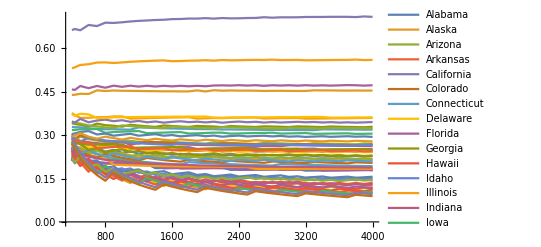

```mathematica
ListPlot[
Transpose[relativeVoterInStateDecisiveProbability],
Joined->True,PlotRange->All
]
```

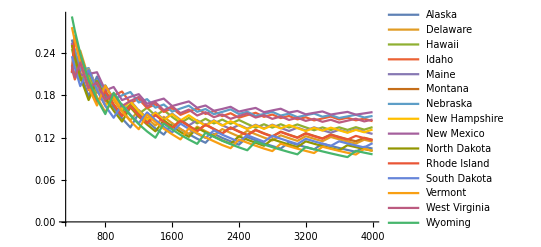

```mathematica
ListPlot[
KeySelect[Transpose[relativeVoterInStateDecisiveProbability],MemberQ[smallest15States,#]&],
Joined->True,PlotRange->All
]
```

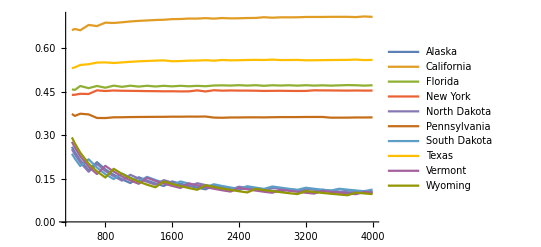

```mathematica
ListPlot[
KeySelect[Transpose[relativeVoterInStateDecisiveProbability],MemberQ[largest5Smallest5States,#]&],
Joined->True,PlotRange->All
]
```